# Week02

### Gerardo Durán Martín MTH739P

Sum of arrays. Create a module myarraysum[v] which takes as input an array (vector) and
returns as output the sum of its elements. Test the function with a small-sized array. Did you
know that you could use the Mathematica function Total[] for similar purposes?

```mathematica
myArraySum[V0_] := Module[{V = V0, nElements = Length[V0]},
total = 0;
Do[total = total + V[[i]], {i, 1, nElements}];
total
]
myArraySum[{1,3,4}]
```

8

Frequencies. Create a module mycount[v] which takes as input a vector v containing
integers in the range [1, 10] and returns as output a vector countv of 10 elements, where
countv[[1]] is the number of times the number 1 appears in the input vector v, countv[[2]]
is the number of times the number 2 appears in the input vector v, and so forth.

```mathematica
myCount[V0_] := Module[{V = V0, nElements=Length[V0]},
count = Range[10] * 0;
Do[val = V[[i]];
    count = ReplacePart[count, val->count[[val]] + 1],
 {i, 1, nElements}];
count
]
myCount[{1, 1, 3, 4, 5, 1, 2, 3, 4}]
```

{3,1,2,2,1,0,0,0,0,0}

```mathematica
vTest = RandomInteger[{1, 10}, 5]
myCount[vTest]
```

{5,4,3,4,1}

{1,0,1,2,1,0,0,0,0,0}

(a) When your implementation of mycount[v] works, can you generalise the module to
work with input vectors whose values are integers in any arbitrary interval? Did you know
that you could use the Mathematica function BinCounts[] for similar purposes?

```mathematica
myCount[V0_] := Module[{V = V0, nElements=Length[V0],maxV = Max[V0]},
count = Range[maxV] * 0;
Do[val = V[[i]];
    count = ReplacePart[count, val->count[[val]] + 1],
 {i, 1, nElements}];
count
]
myCount[{1, 1, 1, 2, 3, 3}]
myCount[{1, 1, 1, 2, 3, 3, 10}]
```

{3,1,2}

{3,1,2,0,0,0,0,0,0,1}

Try to construct a module myfreq[v] which works similarly but returns the frequency
of each number in the interval[1, 10], i.e.the number of times it appears divided by the
total number of elements in the input vector v.Generalise the module to work with input
vectors whose values are integers in any arbitrary interval

```mathematica
myFreq[V0_] := Module[{V = V0, nElements=Length[V0], maxV = Max[V0]},
count = Range[maxV] * 0;
Do[val = V[[i]];
    count = ReplacePart[count, val->count[[val]] + 1],
 {i, 1, nElements}];
count / nElements
]
myFreq[{1, 1, 1, 2, 3, 3}]
myFreq[{1, 1, 1, 2, 3, 3, 10}]
```

{1/2,1/6,1/3}

{3/7,1/7,2/7,0,0,0,0,0,0,1/7}

```mathematica
Total[%]
```

1

Construct a module mymoment[P, m] that takes as input a vector P which represents a distribution of integer positive numbers (i.e.P[[1]] is the frequency of 1, P[[2]] is the frequency of 2, and so on) and returns the value of the mth moment of the distribution.

```mathematica
myMoment[P0_, m0_] := Module[{P = P0, m=m0, nElements=Length[P0]},
μ =0;
Do[freq= P[[n]]; μ=μ + n^m* freq,{n, 1, nElements}];
μ
]
```

```mathematica
myMoment[myFreq[{1, 1, 1, 2, 3, 3}], 1]
```

11/6

```mathematica
myMoment[myFreq[{1, 1, 1, 2, 3, 3, 10}], 1]
```

3

```mathematica
myMoment[myFreq[{1, 1, 1, 2, 3, 3, 10}], 2]
```

125/7

```mathematica
elements := {1, 1, 1, 2, 3, 3}
freqs1 := myFreq[elements]
V1 =myMoment[freqs1, 2] - myMoment[freqs1, 1]^2
```

29/36

```mathematica
Variance[elements]
```

29/30

Create a non-recursive module that computes the factorial f(n) = n! (e.g.,
using a Do or a While loop). What is the largest value of n you can use as an argument of
your function before encountering arithmetic overflow?

```mathematica
factorial[n0_] := Module[{n=n0},
factVal = 1;
Do[factVal = factVal * i, {i, 1, n}];
factVal
]
factorial[5]
```

120

```mathematica
2^64
```

18446744073709551616

```mathematica
factorial[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
n :=0
fval := 0
```

```mathematica
While[fval < 2^64, n++; fval = factorial[n]]
```

```mathematica
n
```

21

```mathematica
factorial[21]
```

51090942171709440000

```mathematica
factorial[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
plotPois[λ_] := DiscretePlot[λ^n/factorial[n]*Exp[-λ], {n, 0, 20}]
```

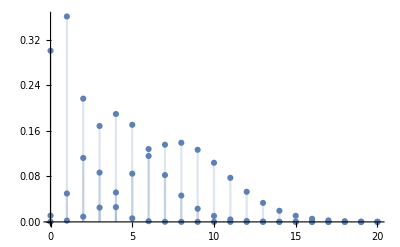

```mathematica
plotPois @{1.2, 4.5, 8.2}
```